# Abbe

### Laser Wellenlänge

```mathematica
λ={632.8,0}10^-9;
```

### Gitter verschieben -> Gitterabstand(~28µm)

```mathematica
d={{28,65,180},0.1}10^-6;
```

### Ordnungen zählen

```mathematica
m={{1,2,3},1};
```

### Numerische Aperatur berechnen

```mathematica
NA = 1.22{(m[[1]]λ[[1]])/d[[1]],(m[[1]]λ[[2]])/d[[1]]+(m[[1]]λ[[1]] d[[2]])/d[[1]]^2}//N;
Grid[NA,Frame->All]
```

0.027572 | 0.0237543 | 0.0128669
0.0000984714 | 0.0000365451 | 7.1483×10^-6

```mathematica
<< ErrorBarPlots`
```

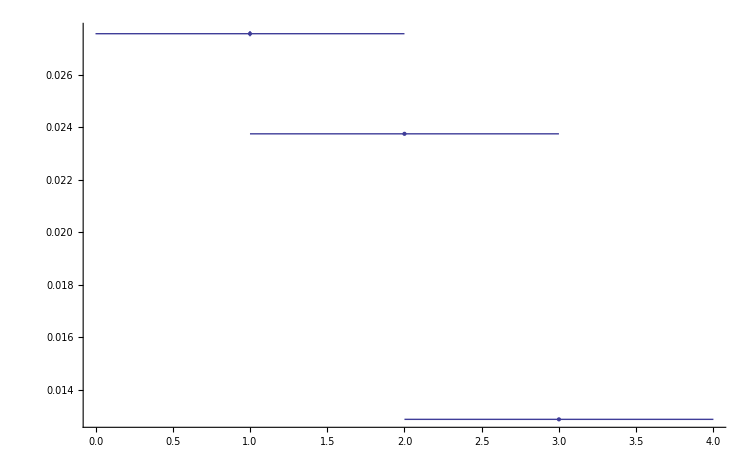

```mathematica
ErrorListPlot[Table[{{m[[1,x]],NA[[1,x]]},ErrorBar[m[[2]],NA[[2,x]]]},{x,1,Length[m[[1]]]}],AxesOrigin->{0,0}]
```